## Ponovitev nekaterih vsebin iz Matematike I

## Integral funkcije

Integrale (nedoločene in določene) v Mathematici računamo z uporabo ukaza Integrate[ ]. Znano je, da se nedoločeni integral nekaterih funkcij ne da izračunati. Za izračun določenega integrala v takem primeru uporabimo ukaz NIntegrate[ ], ki z neko numerično metodo približno izračuna integral.

```mathematica
?Integrate
?NIntegrate
```

```mathematica
Integrate[x^2,x]
Integrate[x^2,{x,0,1}]
```

1. Izračunajte naslednje integrale:
∫x sin(x) ⅆx,
	∫_0^π x sin(x)  ⅆx,
	∫_0^∞ x^2 ⅇ^(-2x) ⅆx,
	∫_0^1 sin (ⅇ^(x^2)) ⅆx.

Rezultati: -x cos(x)+sin(x), π, 1/4, 0.88624.

2. Izračunajte ploščino lika, ki je omejen s krivuljo y = 6/(5 - 4x - x^2) in premicami x = 2, x = 3 ter abscisno osjo.
	Rezultat: S = ln(7/4).

3. Izračunajte prostornino in površino plašča rotacijskega telesa, ki nastane, če krivuljo y = √(1 - x^2), 0 < x < 1, zavrtimo okoli osi x.
    Rezultati: V = 2π/3, P = 2π

```mathematica
y=Sqrt[1-x^2];
Plot[y,{x,0,1},AspectRatio->Automatic,PlotStyle->{Blue,Thick}]
```

## Funkcijske vrste

## Potenčna vrsta

Limito zaporedja/funkcije izračunamo z ukazom Limit[]. Vsoto vrste izračunamo z ukazom Sum[].

```mathematica
?Limit
?Sum
```

4. Določite območje konvergence potenčne vrste   ∑ _(n=0)^∞ 1/(√(3n+2))(3x+1)^n.
	Rezultat: [-2/3,0).

5. Poiščite konvergenčno območje funkcijske vrste   ∑ _(n=1)^∞ 1/n((2x)/(x-2))^n. Uporabite ustrezno substitucijo za prevedbo na potenčno vrsto.
	 Rezultat:( -2 ,2/3 ].

## Taylorjeva vrsta

Ukaz Series[] razvije funkcijo v Taylorjevo vrsto, ki pa še ni uporabna za vstavljanje števil. Ukaz Normal[Series[..]] bo iz vrste izbrisal  ostanek in napravil navaden polinom, v katerega se lahko vstavi število x.

```mathematica
?Series
?Normal
```

Vrednosti funkcije/zaporedja tabeliramo z ukazom Table[].

```mathematica
?Table
```

```mathematica
Clear[a,n]
a[n_]:=1/n;
Table[a[n],{n,1,10}]
```

6. Naj bo n naravno število,(npr. n=7). Razvijte funkcijo f(x) = sin(x)v Taylorjevo vrsto v okolici točke x_0=0 do vključno potence n
in uporabite tako dobljeno vrsto za izračun vrednosti sin(1°). S spreminjanjem n ugotovite,koliko je potreben n,da bo rezultat natančen do 10^-30.
Rezultat: n=11.

```mathematica
Fuck
```

```mathematica
fF[n_]:= Normal[Series[Sin[x], {x, 0, n}]]
N[fF[11]/.x-> Degree, 30]
Table
```

0.0174524064372835128194189785163

7. Z uporabo ustrezne Taylorjeve vrste izračunajte približno vrednost 29^(1/3)na 5 decimalnih mest natančno.
	Rezultat: 3.07232.

```mathematica
f[x_] :=3(1+x)^(1/3)
Table[N[Normal[Series[f[x], {x, 0, k}]]/.x->2/27, 6], {k, 1, 10}]
```

{3.07407,3.07225,3.07232,3.07232,3.07232,3.07232,3.07232,3.07232,3.07232,3.07232}

Integral funkcije izračunamo z ukazom Integrate[].

```mathematica
?Integrate
```

```mathematica
Integrate[x,{x,0,1}]
```

1/2

```mathematica
Integrate[Sin[x],x]
Integrate[Sin[x],{x,0,Pi}]
```

8. Izračunajte integral ∫_0^1 ⅇ^(x^2) ⅆx tako, da podintegralno funkcijo razvijete v Taylorjevo vrsto do potence x^6.
	Rezultat: 1.45714.

```mathematica
Integrate[E^(x^2),{x, 0, 1}]
Integrate[Normal[Series[E^(x^2), {x, 0, 6}]], {x, 0, 1}]//N
```

1/2 √π Erfi[1]

1.45714

## Fourierova vrsta

Za razvoj funkcij v trigonometrične vrste ima Mathematica vgrajene funkcije.

```mathematica
?FourierSeries
?FourierTrigSeries
?FourierSinSeries
?FourierCosSeries
```

Vse funkcije privzemajo, da funkcije razvijamo na intervalu (-π,π). Razvoj na intervalu (-T/2,T/2) dobimo tako, da v ukaz dodamo opcijo FourierParameters→{1,(2π)/T}.

Funkcijo zlepljeno iz dveh formul se da zapisati z ukazom If[], Which[] ali Piecewise[].

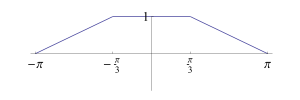
9. Razvijte funkcijo f,ki je podana z grafom na sliki, v Fourierjevo vrsto na intervalu (-π,π) .
-Graphics-

Rezultat:f(x)=2/3 + (Σ^∞)_(n=1)3/(n^2 π^2)(cos(n π)/3-(-1)^n)cos(n x).